Your Title Here

```mathematica
Manipulate[
Module[{spacing,spacingdots,height,p1,p2,p3},
spacing=0.5;
spacingdots=0.4;
height=0.2;

p1=Graphics3D[{
Cuboid[{(d+0.2)+spacing,(d+0.2)+spacing,#*((d+0.2)+spacing)},{-(d+0.2)-spacing,-(d+0.2)-spacing,#*((d+0.2)+spacing)}]&/@{-1,1},
Cuboid[{(d+0.2)+spacing,(d+0.2)+spacing,(d+0.2)+spacing},{-(d+0.2)-spacing,(d+0.2)+spacing,-(d+0.2)-spacing}],
Cuboid[{#*((d+0.2)+spacing),(d+0.2)+spacing,#*((d+0.2)+spacing)},{#*((d+0.2)+spacing),-(d+0.2)-spacing,-#*((d+0.2)+spacing)}]&/@{-1,1},
{RGBColor[0.3,0,0.5],Opacity[0.9*ϵball],Sphere[{0,0,0},d]},
If[ptv,{RGBColor[1,0.7,0.75],Opacity[0.85*Es],Sphere[{0,0,0},(d+0.2)]}]
},Lighting->{{"Ambient",LightGray}},ViewPoint->{1.2,-2.4,1.2},Boxed->False];

p2=Graphics[{
(*Line[{
{7.5spacingdots,0},
{7spacingdots,0},
{7spacingdots-2/7spacingdots,height},
{7spacingdots-4/7spacingdots,-height},
{7spacingdots-6/7spacingdots,height},
{7spacingdots-8/7spacingdots,-height},
{7spacingdots-10/7spacingdots,height},
{7spacingdots-12/7spacingdots,-height},
{7spacingdots-14/7spacingdots,0},
{4.5spacingdots,0}
}],*)

(*Line[{{4.5spacingdots,0},
{4spacingdots,0},
{4spacingdots-2/7spacingdots,height},
{4spacingdots-4/7spacingdots,-height},
{4spacingdots-6/7spacingdots,height},
{4spacingdots-8/7spacingdots,-height},
{4spacingdots-10/7spacingdots,height},
{4spacingdots-12/7spacingdots,-height},
{4spacingdots-14/7spacingdots,0},
{1.5spacingdots,0}}],*)

Line[{{1.5spacingdots,0},
{1spacingdots,0},
{1spacingdots-2/7spacingdots,height},
{1spacingdots-4/7spacingdots,-height},
{1spacingdots-6/7spacingdots,height},
{1spacingdots-8/7spacingdots,-height},
{1spacingdots-10/7spacingdots,height},
{1spacingdots-12/7spacingdots,-height},
{1spacingdots-14/7spacingdots,0},
{-1.5spacingdots,0}}],

(*Line[{{-1.5spacingdots,0},
{-2spacingdots,0},
{-2spacingdots-2/7spacingdots,height},
{-2spacingdots-4/7spacingdots,-height},
{-2spacingdots-6/7spacingdots,height},
{-2spacingdots-8/7spacingdots,-height},
{-2spacingdots-10/7spacingdots,height},
{-2spacingdots-12/7spacingdots,-height},
{-2spacingdots-14/7spacingdots,0},
{-4.5spacingdots,0}}],*)

(*Line[{{-4.5spacingdots,0},
{-5spacingdots,0},
{-5spacingdots-2/7spacingdots,height},
{-5spacingdots-4/7spacingdots,-height},
{-5spacingdots-6/7spacingdots,height},
{-5spacingdots-8/7spacingdots,-height},
{-5spacingdots-10/7spacingdots,height},
{-5spacingdots-12/7spacingdots,-height},
{-5spacingdots-14/7spacingdots,0},
{-7.5spacingdots,0}}],*)

Line[{{7spacingdots-spacingdots,-height-0.1},{6spacingdots,-height-0.4}}],
Line[{{4spacingdots-spacingdots,height+0.1},{3spacingdots,height+0.4}}],
Line[{{0,-height-0.1},{0,-height-0.4}}],
Line[{{-2spacingdots-spacingdots,height+0.1},{-3spacingdots,height+0.4}}],
Line[{{-5spacingdots-spacingdots,-height-0.1},{-6spacingdots,-height-0.4}}],


},Axes->True];

Show[p1,ImageSize->{550,340}]
],
Grid[{
{Control[{{ptv,True,"shield"},{True,False}}],
PaneSelector[{
True->Control[{{W,1,""},{1->" 3D image ",2->" network ",3->" plot "},Setter}],
False->Control[{{W,1,""},{1->" 3D image ",2->" network "},Setter}]
},Dynamic@ptv]},
{Control[{{d,0.3,"diameter of object (m)"},0.1,2,0.1,Appearance->"Labeled"}],SpanFromLeft},
{Control[{{Tball,300,"temperature of ball (K)"},100,1000,10,Appearance->"Labeled"}],SpanFromLeft},
{Control[{{ϵball,0.3,"emissivity of ball"},0.05,0.95,0.05,Appearance->"Labeled"}],SpanFromLeft}
},Alignment->Left],
PaneSelector[{
True->Grid[{{
Style["emissivity",Bold],
Control[{{Esi,0.3,"inner shield"},0.05,0.55,0.01,Appearance->"Labeled",ImageSize->Small}],
PaneSelector[{##&@@Thread[{1,2}->Control[{{Es,0.3,"outer shield"},0.05,0.55,0.01,Appearance->"Labeled",ImageSize->Small}]]},Dynamic@W]
}}]
},Dynamic@ptv]
]
```

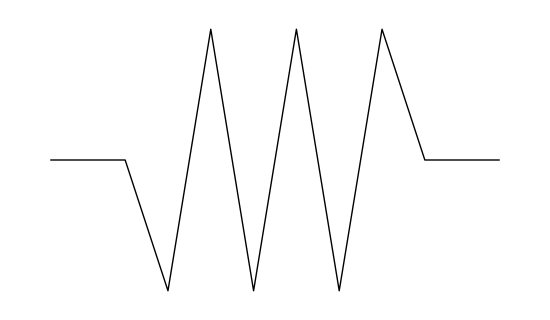

```mathematica
Module[{δx,δy},
δx=0.4;δy=0.2;

Graphics[{
Line[{
{1.5*δx,0},
{δx,0},
{δx-2/7δx,δy},
{δx-4/7δx,-δy},
{δx-6/7δx,δy},
{δx-8/7δx,-δy},
{δx-10/7δx,δy},
{δx-12/7δx,-δy},
{δx-14/7δx,0},
{-1.5*δx,0}
}]
},ImageSize->{550,320}]
]
```

```mathematica
Module[{δx,δy,x0,x1},
δx=0.1;δy=0.2;
x0=0;x1=x0+2*δx;

Graphics[{
(*Line[{#1*δx/2,#2*δy}&@@@{{1,-1},{3,1},{5,-1},{7,1},{9,-1},{11,1}}]*)
Line@FlattenAt[Insert[{{x0,0},{x1,0},{x1+δx/2,-δy},{x1+11*δx/2,δy},{x1+12*δx/2,0},{x1+16*δx/2,0}},{x1+#1*δx/2,#2*δy}&@@@{{1,-1},{3,1},{5,-1},{7,1},{9,-1},{11,1}},4],4]
},ImageSize->{550,320}];
FlattenAt[Insert[{{x0,0},{x1,0},{x1+δx/2,-δy},{x1+11*δx/2,δy},{x1+12*δx/2,0},{x1+16*δx/2,0}},{x1+#1*δx/2,#2*δy}&@@@{{1,-1},{3,1},{5,-1},{7,1},{9,-1},{11,1}},4],4]
]
```

{{0,0},{0.2,0},{0.25,-0.2},{0.25,-0.2},{0.35,0.2},{0.45,-0.2},{0.55,0.2},{0.65,-0.2},{0.75,0.2},{0.75,0.2},{0.8,0},{1.,0}}

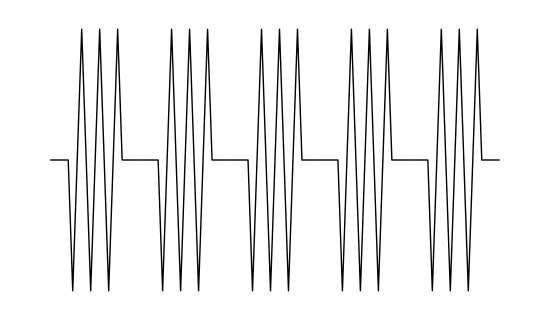

```mathematica
Module[{δx,δy},
δx=0.1;δy=0.2;

Graphics[{
(*Table[Line@FlattenAt[Insert[{{x0,0},{x0+2*δx,0},{(x0+2*δx)+δx/2,-δy},{(x0+2*δx)+11*δx/2,δy},{(x0+2*δx)+12*δx/2,0},{(x0+2*δx)+16*δx/2,0}},{(x0+2*δx)+#1*δx/2,#2*δy}&@@@{{1,-1},{3,1},{5,-1},{7,1},{9,-1},{11,1}},4],4],{x0,-2,2}]*)
Table[Line@FlattenAt[Insert[{{x0,0},{x0+2*δx,0},(*{(x0+2*δx)+δx/2,-δy},*)(*{(x0+2*δx)+11*δx/2,δy},*){(x0+2*δx)+12*δx/2,0},{(x0+2*δx)+16*δx/2,0}},{(x0+2*δx)+#1*δx/2,#2*δy}&@@@{{1,-1},{3,1},{5,-1},{7,1},{9,-1},{11,1}},3],3],{x0,-2,2}]
},ImageSize->{550,320}]
]
```

```mathematica
DeleteDuplicates@FlattenAt[Insert[{{x0,0},{x0+2*δx,0},{(x0+2*δx)+δx/2,-δy},{(x0+2*δx)+11*δx/2,δy},{(x0+2*δx)+12*δx/2,0},{(x0+2*δx)+16*δx/2,0}},{(x0+2*δx)+#1*δx/2,#2*δy}&@@@{{1,-1},{3,1},{5,-1},{7,1},{9,-1},{11,1}},4],4]
```

{{x0,0},{x0+2 δx,0},{x0+(5 δx)/2,-δy},{x0+(7 δx)/2,δy},{x0+(9 δx)/2,-δy},{x0+(11 δx)/2,δy},{x0+(13 δx)/2,-δy},{x0+(15 δx)/2,δy},{x0+8 δx,0},{x0+10 δx,0}}

```mathematica
FlattenAt[Insert[{{x0,0},{x0+2*δx,0},(*{(x0+2*δx)+δx/2,-δy},*)(*{(x0+2*δx)+11*δx/2,δy},*){(x0+2*δx)+12*δx/2,0},{(x0+2*δx)+16*δx/2,0}},{(x0+2*δx)+#1*δx/2,#2*δy}&@@@{{1,-1},{3,1},{5,-1},{7,1},{9,-1},{11,1}},3],3]
```

{{x0,0},{x0+2 δx,0},{x0+(5 δx)/2,-δy},{x0+(7 δx)/2,δy},{x0+(9 δx)/2,-δy},{x0+(11 δx)/2,δy},{x0+(13 δx)/2,-δy},{x0+(15 δx)/2,δy},{x0+8 δx,0},{x0+10 δx,0}}

```mathematica
(x0+2*δx)+δx/2
```

x0+(5 δx)/2

```mathematica
{#1*δx/2,#2*δy}&@@@{{1,-1},{3,1},{5,-1},{7,1},{9,-1},{11,1}}
```

{{δx/2,-δy},{(3 δx)/2,δy},{(5 δx)/2,-δy},{(7 δx)/2,δy},{(9 δx)/2,-δy},{(11 δx)/2,δy}}

```mathematica
FlattenAt[Insert[{{x0,0},{x1,0},{δx/2,-δy},{11*δx/2,δy},{12*δx/2,0},{14*δx/2,0}},{#1*δx/2,#2*δy}&@@@{{1,-1},{3,1},{5,-1},{7,1},{9,-1},{11,1}},4],4]
```

{{x0,0},{x1,0},{δx/2,-δy},{δx/2,-δy},{(3 δx)/2,δy},{(5 δx)/2,-δy},{(7 δx)/2,δy},{(9 δx)/2,-δy},{(11 δx)/2,δy},{(11 δx)/2,δy},{6 δx,0},{7 δx,0}}

```mathematica
Insert[{{0,0},{1,1},{2,2},{3,3},{4,4},{5,5},{6,6}},{x,x},4]
```

{{0,0},{1,1},{2,2},{x,x},{3,3},{4,4},{5,5},{6,6}}

```mathematica
12*x/2+2*x
```

8 x

```mathematica
16*x/2
```

8 x

```mathematica
Manipulate[
Module[{spacing},
spacing=0.5;
Graphics3D[{
(*Cuboid[{(d+0.2)+spacing,(d+0.2)+spacing,-(d+0.2)-spacing},{-(d+0.2)-spacing,-(d+0.2)-spacing,-(d+0.2)-spacing}],
Cuboid[{(d+0.2)+spacing,(d+0.2)+spacing,(d+0.2)+spacing},{-(d+0.2)-spacing,-(d+0.2)-spacing,(d+0.2)+spacing}],*)
Cuboid[{(d+0.2)+spacing,(d+0.2)+spacing,#*((d+0.2)+spacing)},{-(d+0.2)-spacing,-(d+0.2)-spacing,#*((d+0.2)+spacing)}]&/@{-1,1},

Cuboid[{(d+0.2)+spacing,(d+0.2)+spacing,(d+0.2)+spacing},{-(d+0.2)-spacing,(d+0.2)+spacing,-(d+0.2)-spacing}],

Cuboid[{#*((d+0.2)+spacing),(d+0.2)+spacing,#*((d+0.2)+spacing)},{#*((d+0.2)+spacing),-(d+0.2)-spacing,-#*((d+0.2)+spacing)}]&/@{-1,1}
(*Cuboid[{(d+0.2)+spacing,(d+0.2)+spacing,(d+0.2)+spacing},{(d+0.2)+spacing,-(d+0.2)-spacing,-(d+0.2)-spacing}],
Cuboid[{-(d+0.2)-spacing,(d+0.2)+spacing,-(d+0.2)-spacing},{-(d+0.2)-spacing,-(d+0.2)-spacing,(d+0.2)+spacing}]*)
},Lighting->{{"Ambient",RGBColor[0.86,0.86,0.86]}},ViewPoint->{1.2,-2.4,1.2},Boxed->False,Axes->True,AxesLabel->{"x","y","z"},ImageSize->{550,340}]
],
Control[{{d,0.3,"diameter of object (m)"},0.1,2,0.1,Appearance->"Labeled"}]
]
```

```mathematica
Manipulate[
Module[{spacing},
spacing=0.5;
Graphics3D[{
Cuboid[{(d+0.2)+spacing,(d+0.2)+spacing,#*((d+0.2)+spacing)},{-(d+0.2)-spacing,-(d+0.2)-spacing,#*((d+0.2)+spacing)}]&/@{-1,1},
Cuboid[{(d+0.2)+spacing,(d+0.2)+spacing,(d+0.2)+spacing},{-(d+0.2)-spacing,(d+0.2)+spacing,-(d+0.2)-spacing}],
Cuboid[{#*((d+0.2)+spacing),(d+0.2)+spacing,#*((d+0.2)+spacing)},{#*((d+0.2)+spacing),-(d+0.2)-spacing,-#*((d+0.2)+spacing)}]&/@{-1,1}
},Lighting->{{"Ambient",LightGray}},ViewPoint->{1.2,-2.4,1.2},Boxed->False,ImageSize->{550,340}]
],
Control[{{d,0.3,"diameter of object (m)"},0.1,2,0.1,Appearance->"Labeled"}]
]
```

```mathematica
RGBColor[0.86,0.86,0.86]
```

RGBColor[0.86, 0.86, 0.86]

GrayLevel[0.85]





```mathematica
LightGray
```

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

Contributed by: XXXX